# Prepare LVK posteriors on z, m1 and m2

Davi C. Rodrigues Oct/2023

This  code can do the following:
  i. From the website “https://www.atlas.aei.uni-hannover.de/work/sumit.kumar/Data/GWTC_posterior_samples_cosmo/”, it selects the 72 relevant events and download the corresponding h5 files.
  ii. Exports the relevant data from the downloaded files as a single mx file. Relevant data are z, m1 and m2 data. This mx file is much faster for Mathematica to deal with than the original h5 files. Also, it is much more compact.

This notebook is expected to be in the input folder.

## Download preparation and execution

```mathematica
SetDirectory[NotebookDirectory[]]; 
pathOut = FileNameJoin[{"..", "output"}];
downloadDirectory = FileNameJoin[{NotebookDirectory[], "lvk_posteriors_h5"}]; (*Where the files will be downloaded, thus inside the input folder.*)

(*Stept 0: importing the events names*)
events = Import[FileNameJoin[{pathOut, "dataGWevents.csv"}]]// Drop[#, 1] & // Sort;
datasetEvents = Import[FileNameJoin[{pathOut, "dataGWevents.csv"}], "Dataset", "HeaderLines" -> {1, 1}]; (*Dataset version of events.*)
eventNames = events[[All, 1]];

(* Step 1: Import the webpage content *)
webpageURL = "https://www.atlas.aei.uni-hannover.de/work/sumit.kumar/Data/GWTC_posterior_samples_cosmo/";
webpageContent = Import[webpageURL];

(* Step 2: Extract and filter links based on event names *)
links = StringCases[webpageContent, 
   RegularExpression["(IGWN-GWTC[^\\s]+\\.h5)"] :> "$1"];

filteredLinks = Select[links, StringContainsQ[#, eventNames] &];

(* Step 3: Download filtered ".h5" files.   ** UNCOMMENT TO DOWNLOAD ** *)

(*SetDirectory[downloadDirectory];

Do[
  URLDownload[webpageURL <> link, FileNameJoin[{downloadDirectory, link}]],
  {link, filteredLinks}
]*)
```

## Exporting the relevant data from the h5 files as a single mx file

```mathematica
SetDirectory[downloadDirectory];
filesh5 = FileNames["*.h5"];
Clear[file];
file[i_] := First@Select[filesh5, StringContainsQ[#, eventNames[[i]]] &];

Clear[posterior, csvTable];
posterior[i_] := Import[file[i], "/C01:Mixed/posterior_samples"];

h5Table[i_] := posterior[i][[All, {"redshift", "mass_1_source", "mass_2_source"} ]]; 

(*
  OLD CODE FOR EXPORTING TO CSV VERY SLOW

  csvTable[i_] := csvTable[i] = {#["redshift"], #["mass_1_source"], #["mass_2_source"]} & /@ 
    posterior[i][[All, {"redshift", "mass_1_source", "mass_2_source"} ]] // 
    Prepend[#, {"redshift", "mass_1_source", "mass_2_source"}] &;
    
  filenameExport[i_] := "zm1m2-" <> StringTake[file[i], {6,-4}] <> ".csv";
*)


(* Defines file and zm1m2 in the LVK context. All the data from the LVK context will be exported. *)

Do[LVK`file[i] = file[i], {i,72}];
Monitor[Do[LVK`zm1m2[i] = h5Table[i], {i,72}],i] // EchoTiming
```

1037.

```mathematica
DumpSave[".."<>"LVKzm1m2All.mx",  "LVK`"] // EchoTiming
```

25.4945

{LVK`}

## Testing

### GW190805 (perfect match)

```mathematica
data = Import["IGWN-GWTC2p1-v2-GW190805_211137_PEDataRelease_mixed_cosmo.h5"];
```

```mathematica
post1 = Import["IGWN-GWTC2p1-v2-GW190805_211137_PEDataRelease_mixed_cosmo.h5", "/C01:IMRPhenomXPHM/posterior_samples"];
post2 = Import["IGWN-GWTC2p1-v2-GW190805_211137_PEDataRelease_mixed_cosmo.h5", "/C01:Mixed/posterior_samples"];
post3 = Import["IGWN-GWTC2p1-v2-GW190805_211137_PEDataRelease_mixed_cosmo.h5", "/C01:SEOBNRv4PHM/posterior_samples"];
```

45.7464

0.932976

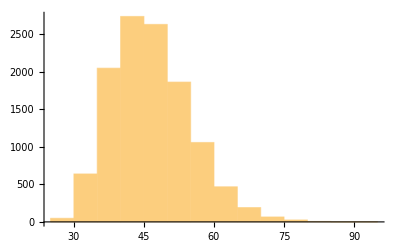
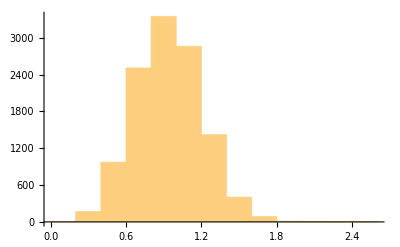

{46.1699,-11.2345,15.4309}

{0.920592,-0.400923,0.431276}

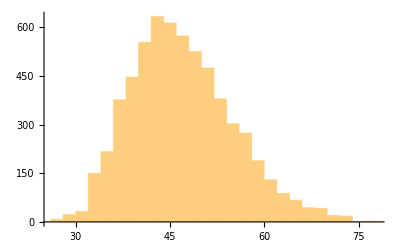
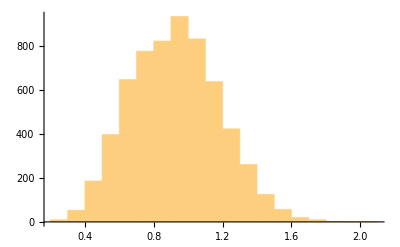

46.6077

0.893883

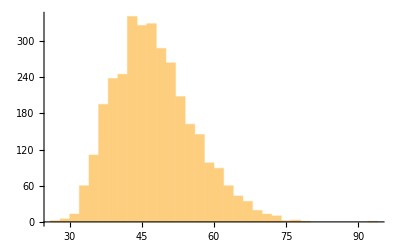
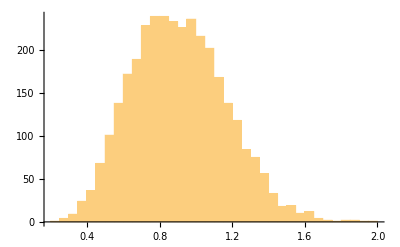

```mathematica
{
  datam1p1 = #["mass_1_source"] & /@ post1;
  Echo@Median[datam1p1];
  Histogram[datam1p1]
,
  datazp1 = #["redshift"] & /@ post1;
  Echo@Median[datazp1];
  Histogram[datazp1]
}

{
  datam1p2 = #["mass_1_source"] & /@ post2;
  Echo[{Median[datam1p2], Quantile[datam1p2, 0.05]- Median[datam1p2], Quantile[datam1p2, 0.95]- Median[datam1p2]}];
  Histogram[datam1p2]
,
  datazp2 = #["redshift"] & /@ post2;
  Echo[{Median[datazp2], Quantile[datazp2, 0.05]- Median[datazp2], Quantile[datazp2, 0.95]- Median[datazp2]}];
  Histogram[datazp2]
}

{
  datam1p3 = #["mass_1_source"] & /@ post3;
  Echo@Median[datam1p3];
  Histogram[datam1p3]
  ,
  datazp3 = #["redshift"] & /@ post3;
  Echo@Median[datazp3];
  Histogram[datazp3]
}
```

### GW150914 (small difference)

```mathematica
eventNames[[1]]
```

GW150914

```mathematica
Clear[file]
file[i_] := First@Select[filesh5, StringContainsQ[#, eventNames[[i]]] &]
```

```mathematica
post1 = Import[file[1], "/C01:IMRPhenomXPHM/posterior_samples"];
post2 = Import[file[1], "/C01:Mixed/posterior_samples"];
post3 = Import[file[1], "/C01:SEOBNRv4PHM/posterior_samples"];
```

34.8957

0.0962973

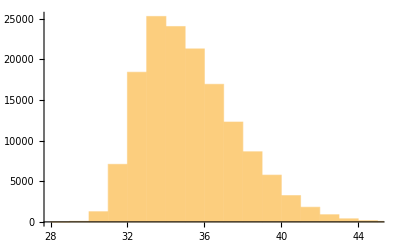
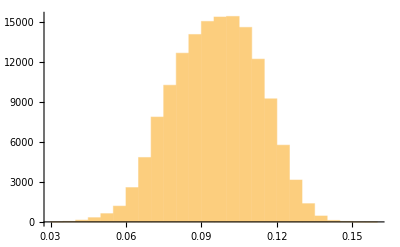

{34.5953,-2.56697,4.49066}

{0.0998053,-0.0321791,0.026798}

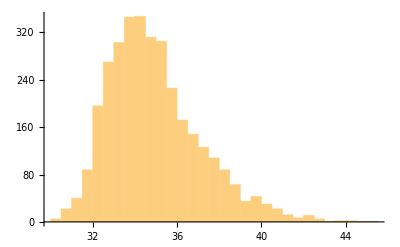
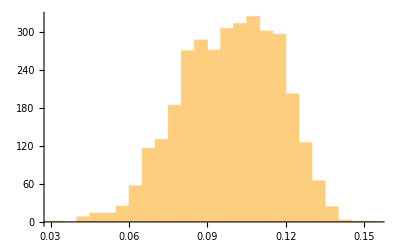

34.2751

0.10361

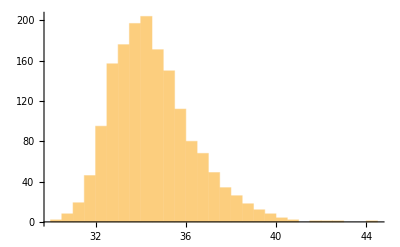
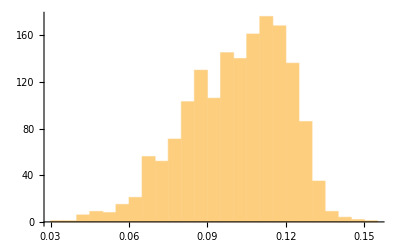

```mathematica
{
  datam1p1 = #["mass_1_source"] & /@ post1;
  Echo@Median[datam1p1];
  Histogram[datam1p1]
,
  datazp1 = #["redshift"] & /@ post1;
  Echo@Median[datazp1];
  Histogram[datazp1]
}

{
  datam1p2 = #["mass_1_source"] & /@ post2;
  Echo[{Median[datam1p2], Quantile[datam1p2, 0.05]- Median[datam1p2], Quantile[datam1p2, 0.95]- Median[datam1p2]}];
  Histogram[datam1p2]
,
  datazp2 = #["redshift"] & /@ post2;
  Echo[{Median[datazp2], Quantile[datazp2, 0.05]- Median[datazp2], Quantile[datazp2, 0.95]- Median[datazp2]}];
  Histogram[datazp2]
}

{
  datam1p3 = #["mass_1_source"] & /@ post3;
  Echo@Median[datam1p3];
  Histogram[datam1p3]
  ,
  datazp3 = #["redshift"] & /@ post3;
  Echo@Median[datazp3];
  Histogram[datazp3]
}
```

### GW151012 (small difference)

```mathematica
eventNames[[2]]
```

GW151012

```mathematica
post1 = Import[file[2], "/C01:IMRPhenomXPHM/posterior_samples"];
post2 = Import[file[2], "/C01:Mixed/posterior_samples"];
post3 = Import[file[2], "/C01:SEOBNRv4PHM/posterior_samples"];
```

24.9921

0.19371

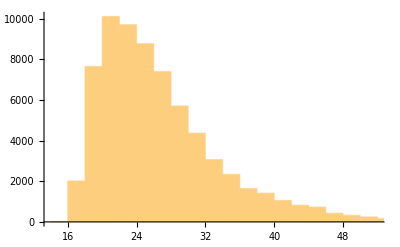
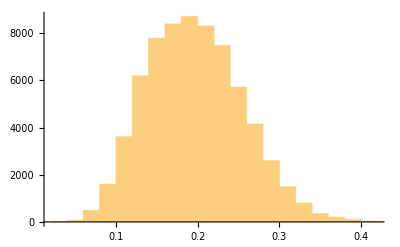

{24.7769,-6.26188,14.5142}

{0.19823,-0.090366,0.108479}

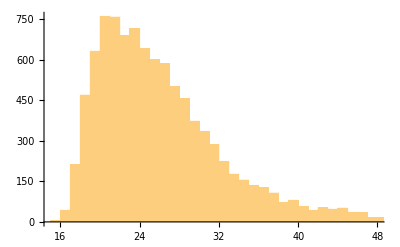
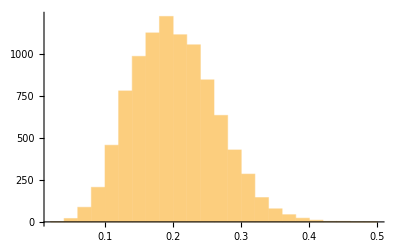

24.3276

0.207518

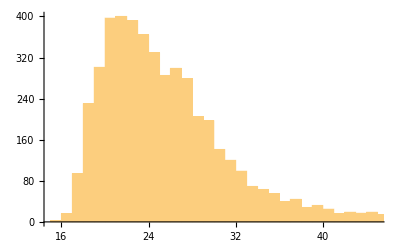
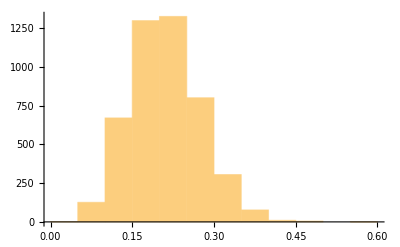

```mathematica
{
  datam1p1 = #["mass_1_source"] & /@ post1;
  Echo@Median[datam1p1];
  Histogram[datam1p1]
,
  datazp1 = #["redshift"] & /@ post1;
  Echo@Median[datazp1];
  Histogram[datazp1]
}

{
  datam1p2 = #["mass_1_source"] & /@ post2;
  Echo[{Median[datam1p2], Quantile[datam1p2, 0.05]- Median[datam1p2], Quantile[datam1p2, 0.95]- Median[datam1p2]}];
  Histogram[datam1p2]
,
  datazp2 = #["redshift"] & /@ post2;
  Echo[{Median[datazp2], Quantile[datazp2, 0.05]- Median[datazp2], Quantile[datazp2, 0.95]- Median[datazp2]}];
  Histogram[datazp2]
}

{
  datam1p3 = #["mass_1_source"] & /@ post3;
  Echo@Median[datam1p3];
  Histogram[datam1p3]
  ,
  datazp3 = #["redshift"] & /@ post3;
  Echo@Median[datazp3];
  Histogram[datazp3]
}
```

```mathematica
datasetEvents[{2}]
```

There is a small discrepancy

### GW190521 (perfect match)

```mathematica
eventNames[[20]]
```

GW190521_030229

```mathematica
post1 = Import[file[20], "/C01:IMRPhenomXPHM/posterior_samples"];
post2 = Import[file[20], "/C01:Mixed/posterior_samples"];
post3 = Import[file[20], "/C01:SEOBNRv4PHM/posterior_samples"];
```

Import::general: No dataset associated with name /C01:SEOBNRv4PHM/posterior_samples

98.4043

0.556044

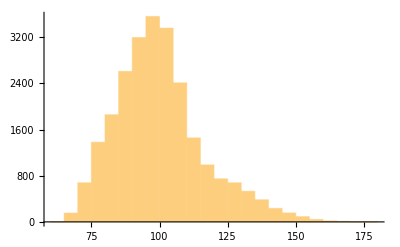
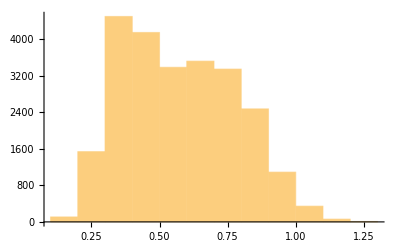

{98.4043,-21.71,33.5863}

{0.556044,-0.269598,0.360829}

{-Graphics-,-Graphics-}

Median[$Failed]

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Histogram::ldata: $Failed is not a valid dataset or list of datasets.

Median[$Failed]

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Histogram::ldata: $Failed is not a valid dataset or list of datasets.

{Histogram[$Failed],Histogram[$Failed]}

```mathematica
{
  datam1p1 = #["mass_1_source"] & /@ post1;
  Echo@Median[datam1p1];
  Histogram[datam1p1]
,
  datazp1 = #["redshift"] & /@ post1;
  Echo@Median[datazp1];
  Histogram[datazp1]
}

{
  datam1p2 = #["mass_1_source"] & /@ post2;
  Echo[{Median[datam1p2], Quantile[datam1p2, 0.05]- Median[datam1p2], Quantile[datam1p2, 0.95]- Median[datam1p2]}];
  Histogram[datam1p2]
,
  datazp2 = #["redshift"] & /@ post2;
  Echo[{Median[datazp2], Quantile[datazp2, 0.05]- Median[datazp2], Quantile[datazp2, 0.95]- Median[datazp2]}];
  Histogram[datazp2]
}

{
  datam1p3 = #["mass_1_source"] & /@ post3;
  Echo@Median[datam1p3];
  Histogram[datam1p3]
  ,
  datazp3 = #["redshift"] & /@ post3;
  Echo@Median[datazp3];
  Histogram[datazp3]
}
```

```mathematica
datasetEvents[[1]] // Keys // Normal
```

{redshift,redshift_lower,redshift_upper,mass_1_source,mass_1_source_lower,mass_1_source_upper,mass_2_source,mass_2_source_lower,mass_2_source_upper}

```mathematica
datasetEvents[{20}]
```

### GW190720 (perfect match)

```mathematica
eventNames[[30]]
```

GW190720_000836

```mathematica
post1 = Import[file[30], "/C01:IMRPhenomXPHM/posterior_samples"];
post2 = Import[file[30], "/C01:Mixed/posterior_samples"];
post3 = Import[file[30], "/C01:SEOBNRv4PHM/posterior_samples"];
```

13.9522

0.154257

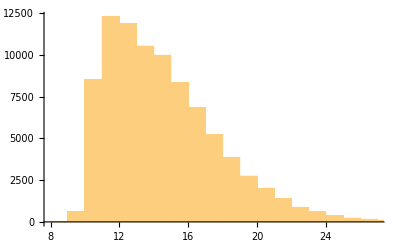
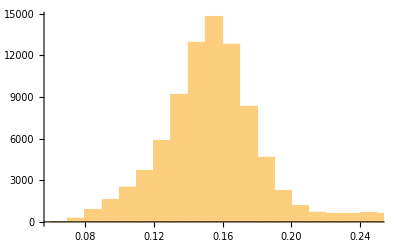

{14.2073,-3.30016,5.58285}

{0.157203,-0.0497795,0.113893}

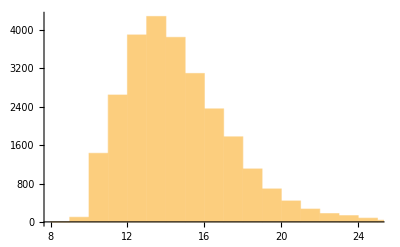
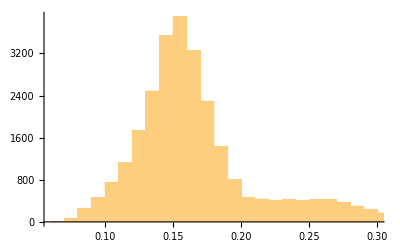

14.3376

0.162472

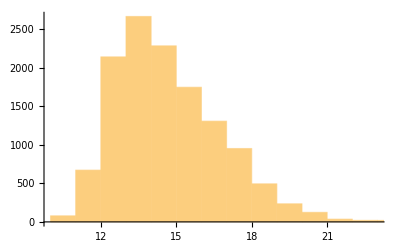
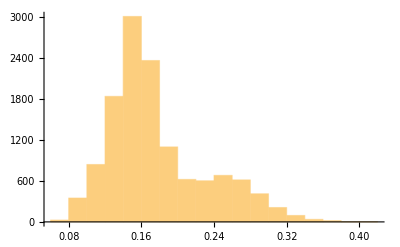

```mathematica
{
  datam1p1 = #["mass_1_source"] & /@ post1;
  Echo@Median[datam1p1];
  Histogram[datam1p1]
,
  datazp1 = #["redshift"] & /@ post1;
  Echo@Median[datazp1];
  Histogram[datazp1]
}

{
  datam1p2 = #["mass_1_source"] & /@ post2;
  Echo[{Median[datam1p2], Quantile[datam1p2, 0.05]- Median[datam1p2], Quantile[datam1p2, 0.95]- Median[datam1p2]}];
  Histogram[datam1p2]
,
  datazp2 = #["redshift"] & /@ post2;
  Echo[{Median[datazp2], Quantile[datazp2, 0.05]- Median[datazp2], Quantile[datazp2, 0.95]- Median[datazp2]}];
  Histogram[datazp2]
}

{
  datam1p3 = #["mass_1_source"] & /@ post3;
  Echo@Median[datam1p3];
  Histogram[datam1p3]
  ,
  datazp3 = #["redshift"] & /@ post3;
  Echo@Median[datazp3];
  Histogram[datazp3]
}
```

```mathematica
datasetEvents[{30}]
```

### GW190917 (perfect match)

```mathematica
eventNames[[70]]
```

GW190917_114630

```mathematica
post1 = Import[file[70], "/C01:IMRPhenomXPHM/posterior_samples"];
post2 = Import[file[70], "/C01:Mixed/posterior_samples"];
post3 = Import[file[70], "/C01:SEOBNRv4PHM/posterior_samples"];
```

Import::general: No dataset associated with name /C01:SEOBNRv4PHM/posterior_samples

9.72075

0.14682

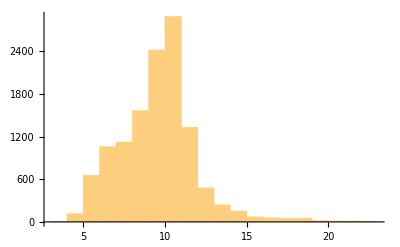
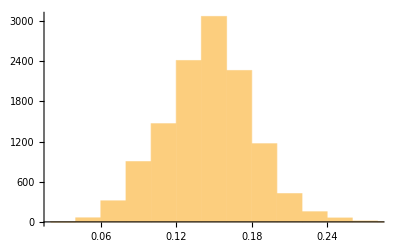

{9.72443,-3.91263,3.46023}

{0.146893,-0.0595608,0.0537581}

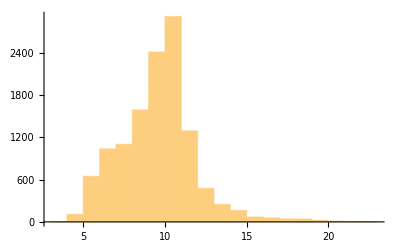
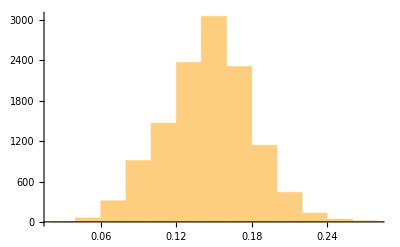

Median[$Failed]

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Histogram::ldata: $Failed is not a valid dataset or list of datasets.

Median[$Failed]

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Histogram::ldata: $Failed is not a valid dataset or list of datasets.

{Histogram[$Failed],Histogram[$Failed]}

```mathematica
{
  datam1p1 = #["mass_1_source"] & /@ post1;
  Echo@Median[datam1p1];
  Histogram[datam1p1]
,
  datazp1 = #["redshift"] & /@ post1;
  Echo@Median[datazp1];
  Histogram[datazp1]
}

{
  datam1p2 = #["mass_1_source"] & /@ post2;
  Echo[{Median[datam1p2], Quantile[datam1p2, 0.05]- Median[datam1p2], Quantile[datam1p2, 0.95]- Median[datam1p2]}];
  Histogram[datam1p2]
,
  datazp2 = #["redshift"] & /@ post2;
  Echo[{Median[datazp2], Quantile[datazp2, 0.05]- Median[datazp2], Quantile[datazp2, 0.95]- Median[datazp2]}];
  Histogram[datazp2]
}

{
  datam1p3 = #["mass_1_source"] & /@ post3;
  Echo@Median[datam1p3];
  Histogram[datam1p3]
  ,
  datazp3 = #["redshift"] & /@ post3;
  Echo@Median[datazp3];
  Histogram[datazp3]
}
```

```mathematica
datasetEvents[{70}]
```